## Building Llama.cpp

cd <*NotebookDirectory[]*>
git clone https://github.com/ggerganov/llama.cpp
cd llama.cpp
mkdir build
cd build
/opt/homebrew/bin/cmake -DLLAMA_STATIC=OFF -DBUILD_SHARED_LIBS=ON -DLLAMA_METAL=ON ..
/opt/homebrew/bin/cmake --build . --config Release
/opt/homebrew/bin/cmake --install . --prefix install

Cloning into 'llama.cpp'...

-- The C compiler identification is AppleClang 15.0.0.15000100

-- The CXX compiler identification is AppleClang 15.0.0.15000100

-- Detecting C compiler ABI info

-- Detecting C compiler ABI info - done

-- Check for working C compiler: /Applications/Xcode.app/Contents/Developer/Toolchains/XcodeDefault.xctoolchain/usr/bin/cc - skipped

-- Detecting C compile features

-- Detecting C compile features - done

-- Detecting CXX compiler ABI info

-- Detecting CXX compiler ABI info - done

-- Check for working CXX compiler: /Applications/Xcode.app/Contents/Developer/Toolchains/XcodeDefault.xctoolchain/usr/bin/c++ - skipped

-- Detecting CXX compile features

-- Detecting CXX compile features - done

-- Found Git: /usr/bin/git (found version "2.39.3 (Apple Git-145)")

-- Performing Test CMAKE_HAVE_LIBC_PTHREAD

-- Performing Test CMAKE_HAVE_LIBC_PTHREAD - Success

-- Found Threads: TRUE

-- Accelerate framework found

-- Metal framework found

-- Warning: ccache not found - consider installing it or use LLAMA_CCACHE=OFF

-- CMAKE_SYSTEM_PROCESSOR: arm64

-- ARM detected

-- Performing Test COMPILER_SUPPORTS_FP16_FORMAT_I3E

-- Performing Test COMPILER_SUPPORTS_FP16_FORMAT_I3E - Failed

-- Configuring done (0.5s)

CMake Warning (dev) at CMakeLists.txt:869 (install):

Target llama has RESOURCE files but no RESOURCE DESTINATION.

This warning is for project developers.  Use -Wno-dev to suppress it.

-- Generating done (0.2s)

-- Build files have been written to: /Users/christopher/git/LlamaLink/llama.cpp/build

[  1%] Building C object CMakeFiles/ggml.dir/ggml.c.o

[  2%] Building C object CMakeFiles/ggml.dir/ggml-alloc.c.o

[  3%] Building C object CMakeFiles/ggml.dir/ggml-backend.c.o

[  4%] Building C object CMakeFiles/ggml.dir/ggml-quants.c.o

[  4%] Building C object CMakeFiles/ggml.dir/ggml-metal.m.o

[  4%] Built target ggml

[  5%] Linking C static library libggml_static.a

[  5%] Built target ggml_static

[  6%] Linking C shared library libggml_shared.dylib

[  6%] Built target ggml_shared

[  7%] Building CXX object CMakeFiles/llama.dir/llama.cpp.o

[  8%] Linking CXX shared library libllama.dylib

[  8%] Built target llama

[  9%] Generating build details from Git

-- Found Git: /usr/bin/git (found version "2.39.3 (Apple Git-145)")

[ 10%] Building CXX object common/CMakeFiles/build_info.dir/build-info.cpp.o

[ 10%] Built target build_info

[ 11%] Building CXX object common/CMakeFiles/common.dir/common.cpp.o

[ 12%] Building CXX object common/CMakeFiles/common.dir/sampling.cpp.o

[ 13%] Building CXX object common/CMakeFiles/common.dir/console.cpp.o

[ 13%] Building CXX object common/CMakeFiles/common.dir/grammar-parser.cpp.o

[ 14%] Building CXX object common/CMakeFiles/common.dir/train.cpp.o

[ 15%] Linking CXX static library libcommon.a

[ 15%] Built target common

[ 16%] Building CXX object tests/CMakeFiles/test-quantize-fns.dir/test-quantize-fns.cpp.o

[ 17%] Linking CXX executable ../bin/test-quantize-fns

[ 17%] Built target test-quantize-fns

[ 18%] Building CXX object tests/CMakeFiles/test-quantize-perf.dir/test-quantize-perf.cpp.o

[ 19%] Linking CXX executable ../bin/test-quantize-perf

[ 19%] Built target test-quantize-perf

[ 19%] Building CXX object tests/CMakeFiles/test-sampling.dir/test-sampling.cpp.o

[ 20%] Linking CXX executable ../bin/test-sampling

[ 20%] Built target test-sampling

[ 21%] Building CXX object tests/CMakeFiles/test-tokenizer-0-llama.dir/test-tokenizer-0-llama.cpp.o

[ 22%] Linking CXX executable ../bin/test-tokenizer-0-llama

[ 22%] Built target test-tokenizer-0-llama

[ 23%] Building CXX object tests/CMakeFiles/test-tokenizer-0-falcon.dir/test-tokenizer-0-falcon.cpp.o

[ 24%] Linking CXX executable ../bin/test-tokenizer-0-falcon

[ 24%] Built target test-tokenizer-0-falcon

[ 25%] Building CXX object tests/CMakeFiles/test-tokenizer-1-llama.dir/test-tokenizer-1-llama.cpp.o

[ 26%] Linking CXX executable ../bin/test-tokenizer-1-llama

[ 26%] Built target test-tokenizer-1-llama

[ 27%] Building CXX object tests/CMakeFiles/test-tokenizer-1-bpe.dir/test-tokenizer-1-bpe.cpp.o

[ 28%] Linking CXX executable ../bin/test-tokenizer-1-bpe

[ 28%] Built target test-tokenizer-1-bpe

[ 29%] Building CXX object tests/CMakeFiles/test-grammar-parser.dir/test-grammar-parser.cpp.o

[ 30%] Linking CXX executable ../bin/test-grammar-parser

[ 30%] Built target test-grammar-parser

[ 31%] Building CXX object tests/CMakeFiles/test-llama-grammar.dir/test-llama-grammar.cpp.o

[ 32%] Linking CXX executable ../bin/test-llama-grammar

[ 32%] Built target test-llama-grammar

[ 33%] Building CXX object tests/CMakeFiles/test-grad0.dir/test-grad0.cpp.o

[ 34%] Linking CXX executable ../bin/test-grad0

[ 34%] Built target test-grad0

[ 35%] Building CXX object tests/CMakeFiles/test-backend-ops.dir/test-backend-ops.cpp.o

[ 35%] Linking CXX executable ../bin/test-backend-ops

[ 35%] Built target test-backend-ops

[ 36%] Building CXX object tests/CMakeFiles/test-autorelease.dir/test-autorelease.cpp.o

[ 37%] Linking CXX executable ../bin/test-autorelease

[ 37%] Built target test-autorelease

[ 38%] Building CXX object tests/CMakeFiles/test-rope.dir/test-rope.cpp.o

[ 39%] Linking CXX executable ../bin/test-rope

[ 39%] Built target test-rope

[ 40%] Building C object tests/CMakeFiles/test-c.dir/test-c.c.o

[ 41%] Linking C executable ../bin/test-c

[ 41%] Built target test-c

[ 41%] Building CXX object examples/baby-llama/CMakeFiles/baby-llama.dir/baby-llama.cpp.o

[ 42%] Linking CXX executable ../../bin/baby-llama

[ 42%] Built target baby-llama

[ 43%] Building CXX object examples/batched/CMakeFiles/batched.dir/batched.cpp.o

[ 44%] Linking CXX executable ../../bin/batched

[ 44%] Built target batched

[ 45%] Building CXX object examples/batched-bench/CMakeFiles/batched-bench.dir/batched-bench.cpp.o

[ 46%] Linking CXX executable ../../bin/batched-bench

[ 46%] Built target batched-bench

[ 47%] Building CXX object examples/beam-search/CMakeFiles/beam-search.dir/beam-search.cpp.o

[ 48%] Linking CXX executable ../../bin/beam-search

[ 48%] Built target beam-search

[ 49%] Building CXX object examples/benchmark/CMakeFiles/benchmark.dir/benchmark-matmult.cpp.o

[ 50%] Linking CXX executable ../../bin/benchmark

[ 50%] Built target benchmark

[ 51%] Building CXX object examples/convert-llama2c-to-ggml/CMakeFiles/convert-llama2c-to-ggml.dir/convert-llama2c-to-ggml.cpp.o

[ 52%] Linking CXX executable ../../bin/convert-llama2c-to-ggml

[ 52%] Built target convert-llama2c-to-ggml

[ 53%] Building CXX object examples/embedding/CMakeFiles/embedding.dir/embedding.cpp.o

[ 54%] Linking CXX executable ../../bin/embedding

[ 54%] Built target embedding

[ 55%] Building CXX object examples/finetune/CMakeFiles/finetune.dir/finetune.cpp.o

[ 56%] Linking CXX executable ../../bin/finetune

[ 56%] Built target finetune

[ 57%] Building CXX object examples/infill/CMakeFiles/infill.dir/infill.cpp.o

[ 58%] Linking CXX executable ../../bin/infill

[ 58%] Built target infill

[ 59%] Building CXX object examples/llama-bench/CMakeFiles/llama-bench.dir/llama-bench.cpp.o

[ 60%] Linking CXX executable ../../bin/llama-bench

[ 60%] Built target llama-bench

[ 61%] Building CXX object examples/llava/CMakeFiles/llava.dir/llava.cpp.o

[ 62%] Building CXX object examples/llava/CMakeFiles/llava.dir/clip.cpp.o

[ 62%] Built target llava

[ 63%] Linking CXX static library libllava_static.a

[ 63%] Built target llava_static

[ 63%] Linking CXX shared library libllava_shared.dylib

[ 63%] Built target llava_shared

[ 64%] Building CXX object examples/llava/CMakeFiles/llava-cli.dir/llava-cli.cpp.o

[ 65%] Linking CXX executable ../../bin/llava-cli

[ 65%] Built target llava-cli

[ 66%] Building CXX object examples/main/CMakeFiles/main.dir/main.cpp.o

[ 67%] Linking CXX executable ../../bin/main

[ 67%] Built target main

[ 68%] Building CXX object examples/tokenize/CMakeFiles/tokenize.dir/tokenize.cpp.o

[ 69%] Linking CXX executable ../../bin/tokenize

[ 69%] Built target tokenize

[ 70%] Building CXX object examples/parallel/CMakeFiles/parallel.dir/parallel.cpp.o

[ 71%] Linking CXX executable ../../bin/parallel

[ 71%] Built target parallel

[ 72%] Building CXX object examples/perplexity/CMakeFiles/perplexity.dir/perplexity.cpp.o

[ 73%] Linking CXX executable ../../bin/perplexity

[ 73%] Built target perplexity

[ 73%] Building CXX object examples/quantize/CMakeFiles/quantize.dir/quantize.cpp.o

[ 74%] Linking CXX executable ../../bin/quantize

[ 74%] Built target quantize

[ 75%] Building CXX object examples/quantize-stats/CMakeFiles/quantize-stats.dir/quantize-stats.cpp.o

[ 76%] Linking CXX executable ../../bin/quantize-stats

[ 76%] Built target quantize-stats

[ 77%] Building CXX object examples/save-load-state/CMakeFiles/save-load-state.dir/save-load-state.cpp.o

[ 78%] Linking CXX executable ../../bin/save-load-state

[ 78%] Built target save-load-state

[ 79%] Building CXX object examples/simple/CMakeFiles/simple.dir/simple.cpp.o

[ 80%] Linking CXX executable ../../bin/simple

[ 80%] Built target simple

[ 81%] Building CXX object examples/passkey/CMakeFiles/passkey.dir/passkey.cpp.o

[ 82%] Linking CXX executable ../../bin/passkey

[ 82%] Built target passkey

[ 83%] Building CXX object examples/speculative/CMakeFiles/speculative.dir/speculative.cpp.o

[ 84%] Linking CXX executable ../../bin/speculative

[ 84%] Built target speculative

[ 85%] Building CXX object examples/lookahead/CMakeFiles/lookahead.dir/lookahead.cpp.o

[ 86%] Linking CXX executable ../../bin/lookahead

[ 86%] Built target lookahead

[ 87%] Building CXX object examples/lookup/CMakeFiles/lookup.dir/lookup.cpp.o

[ 88%] Linking CXX executable ../../bin/lookup

[ 88%] Built target lookup

[ 89%] Building CXX object examples/train-text-from-scratch/CMakeFiles/train-text-from-scratch.dir/train-text-from-scratch.cpp.o

[ 90%] Linking CXX executable ../../bin/train-text-from-scratch

[ 90%] Built target train-text-from-scratch

[ 91%] Building CXX object examples/imatrix/CMakeFiles/imatrix.dir/imatrix.cpp.o

[ 92%] Linking CXX executable ../../bin/imatrix

[ 92%] Built target imatrix

[ 93%] Building CXX object examples/server/CMakeFiles/server.dir/server.cpp.o

[ 94%] Linking CXX executable ../../bin/server

[ 94%] Built target server

[ 95%] Building CXX object examples/export-lora/CMakeFiles/export-lora.dir/export-lora.cpp.o

[ 96%] Linking CXX executable ../../bin/export-lora

[ 96%] Built target export-lora

[ 97%] Building CXX object pocs/vdot/CMakeFiles/vdot.dir/vdot.cpp.o

[ 98%] Linking CXX executable ../../bin/vdot

[ 98%] Built target vdot

[ 99%] Building CXX object pocs/vdot/CMakeFiles/q8dot.dir/q8dot.cpp.o

[100%] Linking CXX executable ../../bin/q8dot

[100%] Built target q8dot

Success[…]

```mathematica
DeleteObject/@ExternalSessions[]
```

{Null}

## Linking to Llama.cpp

```mathematica
libllamadir=FileNameJoin[{NotebookDirectory[],"llama.cpp","build","install"}];
```

```mathematica
libllama=FileNameJoin[{libllamadir,"lib","libllama.dylib"}];
```

```mathematica
SetEnvironment["GGML_METAL_PATH_RESOURCES"->FileNameJoin[{libllamadir,"bin"}]];
```

```mathematica
boolType="CChar";
tokenType="Integer32";
posType="Integer32";
seqidType="Integer32";
```

struct llama_model_params {
    int32_t n_gpu_layers; // number of layers to store in VRAM
    enum llama_split_mode split_mode; // how to split the model across multiple GPUs

    // main_gpu interpretation depends on split_mode:
    // LLAMA_SPLIT_NONE: the GPU that is used for the entire model
    // LLAMA_SPLIT_ROW: the GPU that is used for small tensors and intermediate results
    // LLAMA_SPLIT_LAYER: ignored
    int32_t main_gpu;

    // proportion of the model (layers or rows) to offload to each GPU, size: LLAMA_MAX_DEVICES
    const float * tensor_split;

    // Called with a progress value between 0.0 and 1.0. Pass NULL to disable.
    // If the provided progress_callback returns true, model loading continues.
    // If it returns false, model loading is immediately aborted.
    llama_progress_callback progress_callback;

    // context pointer passed to the progress callback
    void * progress_callback_user_data;

    // override key-value pairs of the model meta data
    const struct llama_model_kv_override * kv_overrides;

    // Keep the booleans together to avoid misalignment during copy-by-value.
    bool vocab_only; // only load the vocabulary, no weights
    bool use_mmap;   // use mmap if possible
    bool use_mlock;  // force system to keep model in RAM
};

```mathematica
modelParamsStruct={
"n_gpu_layers"->"Integer32",
"split_mode"->"UnsignedInteger32",
"main_gpu"->"Integer32",
"tensor_split"->"RawPointer"::["CFloat"],
"progress_callback"->"OpaqueRawPointer",
"progress_callback_user_data"->"OpaqueRawPointer",
"kv_overrides"->"OpaqueRawPointer",
"vocab_only"->boolType,
"use_mmap"->boolType,
"use_mlock"->boolType
};
```

struct llama_context_params {
    uint32_t seed;              // RNG seed, -1 for random
    uint32_t n_ctx;             // text context, 0 = from model
    uint32_t n_batch;           // prompt processing maximum batch size
    uint32_t n_threads;         // number of threads to use for generation
    uint32_t n_threads_batch;   // number of threads to use for batch processing
    int8_t   rope_scaling_type; // RoPE scaling type, from `enum llama_rope_scaling_type`

    // ref: https://github.com/ggerganov/llama.cpp/pull/2054
    float    rope_freq_base;   // RoPE base frequency, 0 = from model
    float    rope_freq_scale;  // RoPE frequency scaling factor, 0 = from model
    float    yarn_ext_factor;  // YaRN extrapolation mix factor, negative = from model
    float    yarn_attn_factor; // YaRN magnitude scaling factor
    float    yarn_beta_fast;   // YaRN low correction dim
    float    yarn_beta_slow;   // YaRN high correction dim
    uint32_t yarn_orig_ctx;    // YaRN original context size

    ggml_backend_sched_eval_callback cb_eval;
    void * cb_eval_user_data;

    enum ggml_type type_k; // data type for K cache
    enum ggml_type type_v; // data type for V cache

    // Keep the booleans together to avoid misalignment during copy-by-value.
    bool mul_mat_q;   // if true, use experimental mul_mat_q kernels (DEPRECATED - always true)
    bool logits_all;  // the llama_eval() call computes all logits, not just the last one (DEPRECATED - set llama_batch.logits instead)
    bool embedding;   // embedding mode only
    bool offload_kqv; // whether to offload the KQV ops (including the KV cache) to GPU
};

```mathematica
contextParamsStruct={
"seed"->"UnsignedInteger32",
"n_ctx"->"UnsignedInteger32",
"n_batch"->"UnsignedInteger32",
"n_threads"->"UnsignedInteger32",
"n_threads_batch"->"UnsignedInteger32",
"rope_scaling_type"->"Integer8",
"rope_freq_base"->"CFloat",
"rope_freq_scale"->"CFloat",
"yarn_ext_factor"->"CFloat",
"yarn_attn_factor"->"CFloat",
"yarn_beta_fast"->"CFloat",
"yarn_beta_slow"->"CFloat",
"yarn_orig_ctx"->"UnsignedInteger32",
"cb_eval"->"OpaqueRawPointer",
"cb_eval_user_data"->"OpaqueRawPointer",
"type_k"->"UnsignedInteger32",
"type_v"->"UnsignedInteger32",
"mul_mat_q"->boolType,
"logits_all"->boolType,
"embedding"->boolType,
"offload_kqv"->boolType
};
```

typedef struct llama_batch {
    int32_t n_tokens;

    llama_token  *  token;
    float        *  embd;
    llama_pos    *  pos;
    int32_t      *  n_seq_id;
    llama_seq_id ** seq_id;
    int8_t       *  logits;

    // NOTE: helpers for smooth API transition - can be deprecated in the future
    //       for future-proof code, use the above fields instead and ignore everything below
    //
    // pos[i] = all_pos_0 + i*all_pos_1
    //
    llama_pos    all_pos_0;  // used if pos == NULL
    llama_pos    all_pos_1;  // used if pos == NULL
    llama_seq_id all_seq_id; // used if seq_id == NULL
} llama_batch;

```mathematica
batchStruct={
"n_tokens"->"Integer32",
"token"->"RawPointer"::[tokenType],
"embd"->"RawPointer"::["CFloat"],
"pos"->"RawPointer"::[posType],
"n_seq_id"->"RawPointer"::["Integer32"],
"seq_id"->"RawPointer"::["RawPointer"::[seqidType]],
"logits"->"RawPointer"::["Integer8"],

(*below are going to be depricated in the future*)
"all_pos_0"->posType,
"all_pos_1"->posType,
"all_seq_id"->seqidType
};
```

typedef struct llama_token_data {
    llama_token id; // token id
    float logit;    // log-odds of the token
    float p;        // probability of the token
} llama_token_data;

```mathematica
tokenDataStruct={
"id"->tokenType,
"logit"->"CFloat",
"p"->"CFloat"
};
```

typedef struct llama_token_data_array {
    llama_token_data * data;
    size_t size;
    bool sorted;
} llama_token_data_array;

```mathematica
tokenDataArrayStruct={
"data"->"RawPointer"::[Values@tokenDataStruct],
"size"->"CSizeT",
"sorted"->boolType
};
```

```mathematica
backendInitC=ForeignFunctionLoad[libllama,"llama_backend_init",{boolType}->"Void"];
```

```mathematica
modelDefaultParamsC=ForeignFunctionLoad[libllama,"llama_model_default_params",{}->Values@modelParamsStruct];
```

```mathematica
loadModelFromFileC=ForeignFunctionLoad[libllama,"llama_load_model_from_file",{"RawPointer"::["CUnsignedChar"],Values@modelParamsStruct}->"OpaqueRawPointer"];
```

```mathematica
contextDefaultParamsC=ForeignFunctionLoad[libllama,"llama_context_default_params",{}->Values@contextParamsStruct];
```

```mathematica
newContextWithModelC=ForeignFunctionLoad[libllama,"llama_new_context_with_model",{"OpaqueRawPointer",Values@contextParamsStruct}->"OpaqueRawPointer"];
```

```mathematica
nvocabC=ForeignFunctionLoad[libllama,"llama_n_vocab",{"OpaqueRawPointer"}->"Integer32"];
```

```mathematica
nctxC=ForeignFunctionLoad[libllama,"llama_n_ctx",{"OpaqueRawPointer"}->"UnsignedInteger32"];
```

```mathematica
tokenizeC=ForeignFunctionLoad[libllama,"llama_tokenize",{
"OpaqueRawPointer",
"RawPointer"::["CUnsignedChar"],
"Integer32",
"RawPointer"::[tokenType],
"Integer32",
boolType,
boolType
}->"Integer32"
];
```

Based on the std::vector<llama_token> llama_tokenize function in common.cpp

```mathematica
tokenize[model_,input_,addBOS_:True,special_:False]:=
Catch@Module[{inputBytes,inputBuf,bufsize,buf,ntokens,ntokens2},
inputBytes=StringToByteArray[input];
inputBuf=RawMemoryExport[inputBytes,"CUnsignedChar"];
bufsize=Length[inputBytes]+Boole[addBOS];
buf=RawMemoryAllocate[tokenType,bufsize];
ntokens=tokenizeC[model,inputBuf,Length[inputBytes],buf,bufsize,Boole[addBOS],Boole[special]];
If[Negative[ntokens],
bufsize=-ntokens;
buf=RawMemoryAllocate[tokenType,bufsize];
ntokens2=tokenizeC[model,inputBuf,Length[inputBytes],buf,bufsize,Boole[addBOS],Boole[special]];
If[ntokens2=!=-ntokens,Throw[$Failed]];
ntokens=ntokens2;
];
RawMemoryImport[buf,{"List",ntokens}]
]
```

```mathematica
tokenToPieceC=ForeignFunctionLoad[libllama,"llama_token_to_piece",{
"OpaqueRawPointer",
"Integer32",
"RawPointer"::["CUnsignedChar"],
"Integer32"
}->"Integer32"
];
```

Based on the std::string llama_token_to_piece function in common.cpp

```mathematica
detokenize[model_,token_Integer]:=
Catch@Module[{bufsize,buf,nchars,nchars2},
bufsize=8;
buf=RawMemoryAllocate["CUnsignedChar",bufsize];
nchars=tokenToPieceC[model,token,buf,bufsize];
If[Negative[nchars],
bufsize=-nchars;
buf=RawMemoryAllocate["CUnsignedChar",bufsize];
nchars2=tokenToPieceC[model,token,buf,bufsize];
If[nchars2=!=-nchars,Throw[$Failed]];
nchars=nchars2
];
RawMemoryImport[buf,{"String",nchars}]
]
detokenize[model_,tokens_List]:=StringJoin[detokenize[model,#]&/@tokens]
```

TODO: What is the difference between token_to_piece and token_get_text?

```mathematica
tokenGetTextC=ForeignFunctionLoad[libllama,"llama_token_get_text",{"OpaqueRawPointer",tokenType}->"RawPointer"::["CUnsignedChar"]];
```

```mathematica
batchInitC=ForeignFunctionLoad[libllama,"llama_batch_init",{
"Integer32",
"Integer32",
"Integer32"
}->Values@batchStruct
];
```

```mathematica
decodeC=ForeignFunctionLoad[libllama,"llama_decode",{"OpaqueRawPointer",Values@batchStruct}->"Integer32"];
```

```mathematica
getLogitsC=ForeignFunctionLoad[libllama,"llama_get_logits",{"OpaqueRawPointer"}->"RawPointer"::["CFloat"]];
```

```mathematica
getLogitsIthC=ForeignFunctionLoad[libllama,"llama_get_logits_ith",{"OpaqueRawPointer","Integer32"}->"RawPointer"::["CFloat"]];
```

```mathematica
sampleSoftmaxC=ForeignFunctionLoad[libllama,"llama_sample_softmax",{"OpaqueRawPointer","RawPointer"::[Values@tokenDataArrayStruct]}->"Void"];
```

```mathematica
sampleTempC=ForeignFunctionLoad[libllama,"llama_sample_temp",{"OpaqueRawPointer","RawPointer"::[Values@tokenDataArrayStruct],"CFloat"}->"Void"];
```

```mathematica
sampleTokenGreedyC=ForeignFunctionLoad[libllama,"llama_sample_token_greedy",{"OpaqueRawPointer","RawPointer"::[Values@tokenDataArrayStruct]}->tokenType];
```

## Testing

```mathematica
backendInitC[0]
```

```mathematica
modelParams=modelDefaultParamsC[];
```

```mathematica
model=loadModelFromFileC["/Users/christopher/git/LlamaLink/llama-2-7b.Q4_K_M.gguf",modelParams]
```

OpaqueRawPointer[…]

```mathematica
nvocab=nvocabC[model]
```

32000

```mathematica
ctxParams=contextDefaultParamsC[];
```

```mathematica
ctx=newContextWithModelC[model,ctxParams]
```

OpaqueRawPointer[…]

```mathematica
nctx=nctxC[ctx]
```

512

```mathematica
tokens=tokenize[model,"I am good at math. I know that 2+2="]
```

{1,306,626,1781,472,5844,29889,306,1073,393,29871,29906,29974,29906,29922}

```mathematica
batch=batchInitC[512,0,1]
```

{0,RawPointer[…],RawPointer[…],RawPointer[…],RawPointer[…],RawPointer[…],RawPointer[…],0,0,0}

```mathematica
batchKeys=PositionIndex[Keys@batchStruct][[All,1]];
```

```mathematica
batch[[1]]=Length[tokens];
MapIndexed[
({t,i}|->(
RawMemoryWrite[batch[[batchKeys["token"]]],t,i];
RawMemoryWrite[batch[[batchKeys["pos"]]],i,i];
RawMemoryWrite[RawMemoryRead[batch[[batchKeys["seq_id"]]],i],0];
RawMemoryWrite[batch[[batchKeys["n_seq_id"]]],1,i];
RawMemoryWrite[batch[[batchKeys["logits"]]],0,i];
))[#1,First[#2]-1]&,
tokens
];
```

```mathematica
RawMemoryWrite[batch[[batchKeys["logits"]]],1,batch[[batchKeys["n_tokens"]]]-1];
```

```mathematica
decodeC[ctx,batch]
```

0

```mathematica
batch[[batchKeys["n_tokens"]]]
```

15

```mathematica
logits=RawMemoryImport[getLogitsIthC[ctx,14],{"List",nvocab}];
```

```mathematica
tokenDatas=RawMemoryExport[{#-1,logits[[#]],0.0}&/@Range[nvocab],Values@tokenDataStruct];
```

```mathematica
tokenDataArray=RawMemoryExport[{{tokenDatas,nvocab,0}},Values@tokenDataArrayStruct];
```

```mathematica
sampleTokenGreedyC[ctx,tokenDataArray]
```

29946

```mathematica
sampleSoftmaxC[ctx,tokenDataArray]
```

```mathematica
sampleTempC[ctx,tokenDataArray,0.5]
```

```mathematica
RawMemoryRead[tokenDataArray]
```

{RawPointer[…],32000,1}

```mathematica
detokenize[model,#]&/@RawMemoryImport[RawMemoryRead[tokenDataArray][[1]],{"List",nvocab}][[;;10,1]]
```

{4,5, ,2,1,6,3,7,8,9}

```mathematica
RawMemoryImport[RawMemoryRead[tokenDataArray][[1]],{"List",nvocab}][[All,3]]
```

```mathematica
RawMemoryImport[RawMemoryRead[tokenDataArray][[1]],{"List",nvocab}][[All,3]]
```

```mathematica
detokenize[model,30166]
```

​

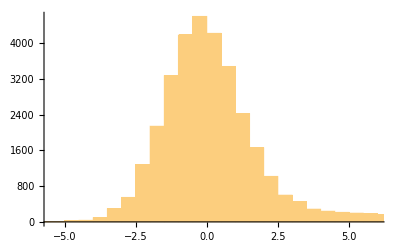

```mathematica
Histogram[logits]
```

```mathematica
TakeLargest[logits->"Index",10]-1
```

{30166,29896,239,243,232,29906,233,229,30243,31102}

```mathematica
tokenStrings[[TakeLargest[logits->"Index",10]-1]]
```

{.b4,k,<0xEB>,<0xEF>,<0xE4>,\,<0xE5>,<0xE1>,ة,程}

```mathematica
tokenStrings[[Ordering[logits,-1][[1]]-1]]
```

.b4

```mathematica
tokenStrings=Table[RawMemoryImport[tokenGetTextC[model,t],"String"],{t,0,nvocab-1}];
```

```mathematica
tokenStrings[[Ordering[logits,-1][[1]]-1]]
```

```mathematica
detokenize[model,Ordering[logits,-1][[1]]-1]
```

​

```mathematica
batchStruct//Column
```

n_tokens→Integer32
token→TypeSpecifier[RawPointer][Integer32]
embd→TypeSpecifier[RawPointer][CFloat]
pos→TypeSpecifier[RawPointer][Integer32]
n_seq_id→TypeSpecifier[RawPointer][Integer32]
seq_id→TypeSpecifier[RawPointer][TypeSpecifier[RawPointer][Integer32]]
logits→TypeSpecifier[RawPointer][Integer8]
all_pos_0→Integer32
all_pos_1→Integer32
all_seq_id→Integer32

```mathematica
StringRiffle[detokenize[model,#]&/@tokenize[model,"Hello! My name is Christopher!"],"|"]
```

| Hello|!| My| name| is| Christopher|!

## C experiments

```mathematica
Needs["CCompilerDriver`"]
```

```mathematica
getSizeTemplate=StringTemplate["#include <llama.h>

size_t `1`() {return sizeof(`2`);}"];
```

```mathematica
getTypeSize[type_]:=
Module[{libpath,fname,ff,res},
fname=StringJoin@RandomChoice[Alphabet[],16];
libpath=CreateLibrary[
getSizeTemplate[fname,type],
CreateUUID[],
"IncludeDirectories"->FileNameJoin[{NotebookDirectory[],"llama.cpp"}]
];
ff=ForeignFunctionLoad[libpath,fname,{}->"CSizeT"];
res=ff[];
DeleteFile[libpath];
res
]
```

```mathematica
getTypeSize["int"]
```

4

```mathematica
getTypeSize["bool"]
```

1

```mathematica
getTypeSize["enum llama_split_mode"]
```

4

```mathematica
getTypeSize["struct llama_model_params"]
```

56